# covfefe Markov Chain

Based on the presentation at https://www.youtube.com/watch?v=JTz4wkD-mxU

### covfefe Markov Chain

```mathematica
states={"Fail","C","CO","COV","COVF","COVFE","COVFEF","COVFEFE"}
```

{Fail,C,CO,COV,COVF,COVFE,COVFEF,COVFEFE}

One for starting state to fail straight away. One for each state except for failure. One for identity on "covfefe".

```mathematica
M={{25/26,1/26,0,0,0,0,0,0},{24/26,1/26,1/26,0,0,0,0,0},{24/26,1/26,0,1/26,0,0,0,0},{24/26,1/26,0,0,1/26,0,0,0},{24/26,1/26,0,0,0,1/26,0,0},{24/26,1/26,0,0,0,0,1/26,0},{24/26,1/26,0,0,0,0,0,1/26},{0,0,0,0,0,0,0,1}};
```

```mathematica
TableForm[M,TableHeadings->{states,states}]
```

| Fail | C | CO | COV | COVF | COVFE | COVFEF | COVFEFE
Fail | 25/26 | 1/26 | 0 | 0 | 0 | 0 | 0 | 0
C | 12/13 | 1/26 | 1/26 | 0 | 0 | 0 | 0 | 0
CO | 12/13 | 1/26 | 0 | 1/26 | 0 | 0 | 0 | 0
COV | 12/13 | 1/26 | 0 | 0 | 1/26 | 0 | 0 | 0
COVF | 12/13 | 1/26 | 0 | 0 | 0 | 1/26 | 0 | 0
COVFE | 12/13 | 1/26 | 0 | 0 | 0 | 0 | 1/26 | 0
COVFEF | 12/13 | 1/26 | 0 | 0 | 0 | 0 | 0 | 1/26
COVFEFE | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1

```mathematica
procCOVFEFE=DiscreteMarkovProcess[1,M]
```

DiscreteMarkovProcess[1,{{25/26,1/26,0,0,0,0,0,0},{12/13,1/26,1/26,0,0,0,0,0},{12/13,1/26,0,1/26,0,0,0,0},{12/13,1/26,0,0,1/26,0,0,0},{12/13,1/26,0,0,0,1/26,0,0},{12/13,1/26,0,0,0,0,1/26,0},{12/13,1/26,0,0,0,0,0,1/26},{0,0,0,0,0,0,0,1}}]

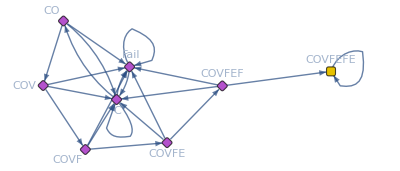

```mathematica
Show[Graph[procCOVFEFE,VertexLabels->Table[i->states[[i]],{i,1,8}]],ImageSize->Full]
```

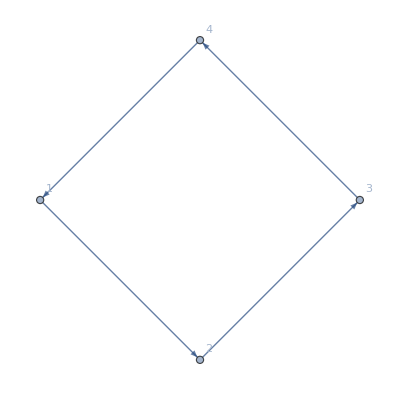

```mathematica
Graph[{1->2,2->3,3->4,4->1},VertexLabels->All]
```

```mathematica
FirstPassageTimeDistribution[procCOVFEFE,8]//Mean
```

8031810176

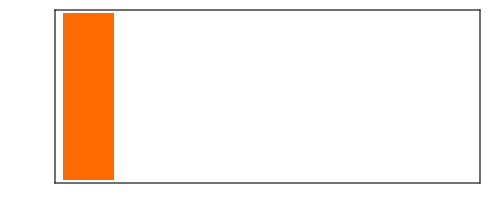
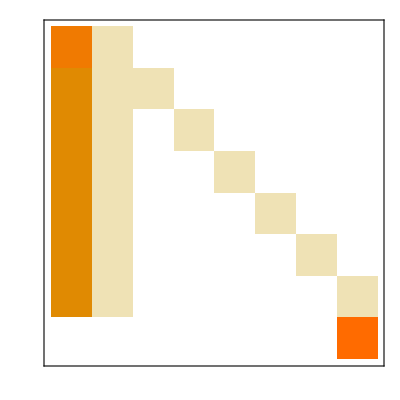
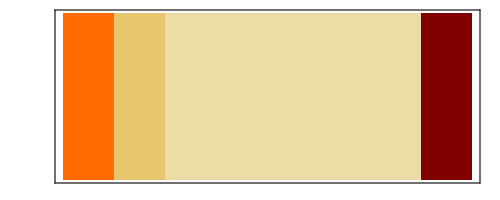
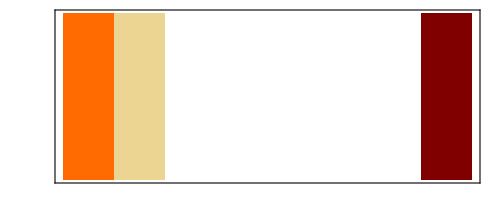
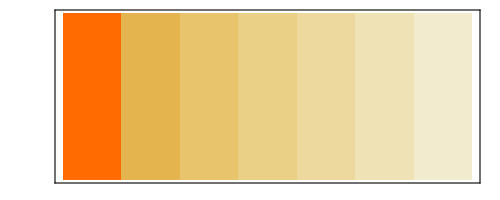
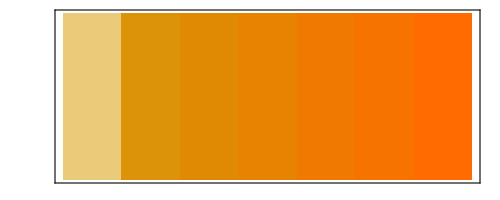
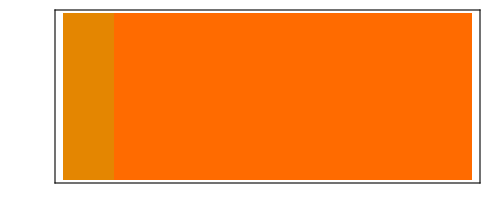
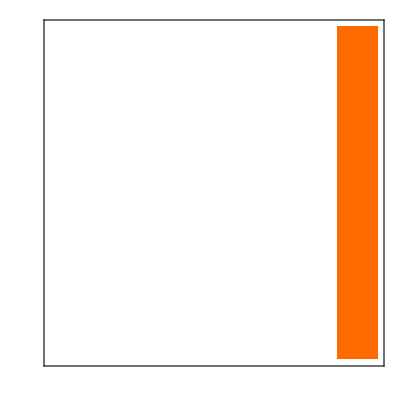
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | -Graphics-
HoldingTimeVariance | -Graphics-
Structural Properties | 
CommunicatingClasses | {8}, {1,…,7}
RecurrentClasses | {8}
TransientClasses | {1,…,7}
AbsorbingClasses | {8}
PeriodicClasses | None
Periods | {}
Irreducible | False
Aperiodic | True
Primitive | False
Transient Properties | 
TransientVisitMean | -Graphics-
TransientVisitVariance | -Graphics-
TransientTotalVisitMean | 7
Limiting Properties | 
ReachabilityProbability | -Graphics-
LimitTransitionMatrix | -Graphics-
Reversible | False

{1.,1.,0.0224305,0.0111299+0.0194242 ⅈ,0.0111299-0.0194242 ⅈ,-0.0112132+0.0192801 ⅈ,-0.0112132-0.0192801 ⅈ,-0.022264}

```mathematica
MarkovProcessProperties[procCOVFEFE]
Eigenvalues[M]//N
```

## Why THH is likely to come earlier than HHH?

THH: 1/2 chance to get heads and void, 1/2 chance to get tails and void, then half chance to get tails and void again.
Similar logic for HHH

```mathematica
THH = {{1/2, 1/2,0,0}, {0, 1/2, 1/2, 0},{0, 1/2,0,1/2},{0,0,0,1}};
HHH = {{1/2, 1/2,0,0}, {1/2, 0, 1/2, 0},{1/2, 0,0,1/2},{0,0,0,1}};
```

Plot this in a table:

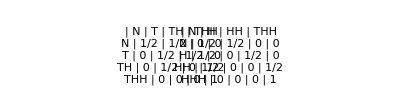

```mathematica
GraphicsRow[{TableForm[THH, TableHeadings -> {{"N", "T", "TH","THH"},{"N", "T", "TH","THH"}}], TableForm[HHH, TableHeadings -> {{"N", "H", "HH","HHH"},{"N", "H", "HH","THH"}}]}]
```

```mathematica
THH // MatrixForm
```

(1/2 | 1/2 | 0 | 0
0 | 1/2 | 1/2 | 0
0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 1)

```mathematica
procTHH = DiscreteMarkovProcess[1,THH];
```

```mathematica
procHHH = DiscreteMarkovProcess[1, HHH];
```

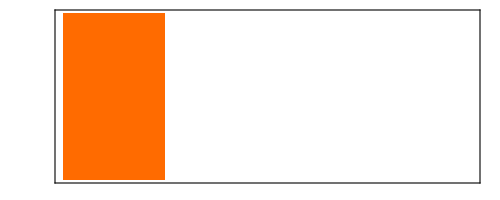
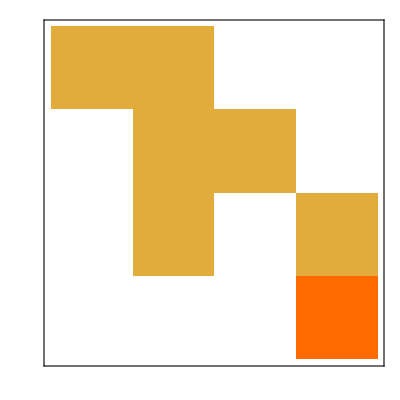
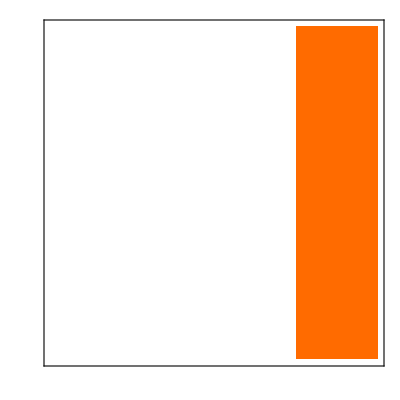
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | {1,1,0,∞}
HoldingTimeVariance | {2,2,0,∞}
Structural Properties | 
CommunicatingClasses | {4}, {2,3}, {1}
RecurrentClasses | {4}
TransientClasses | {2,3}, {1}
AbsorbingClasses | {4}
PeriodicClasses | None
Periods | {}
Irreducible | False
Primitive | False
Aperiodic | True
Transient Properties | 
TransientVisitMean | {4,2,2}
TransientVisitVariance | {28,42,42}
TransientTotalVisitMean | 3
Limiting Properties | 
ReachabilityProbability | {1/2,1,1,1}
LimitTransitionMatrix | -Graphics-
Reversible | False

```mathematica
MarkovProcessProperties[procTHH]
```

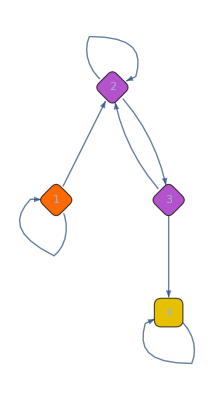
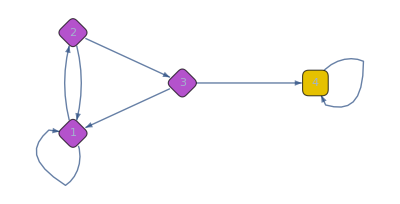

```mathematica
{Graph[procTHH], Graph[procHHH]}
```

```mathematica
FirstPassageTimeDistribution[procTHH,4]//Mean
```

8

```mathematica
FirstPassageTimeDistribution[procHHH,4]//Mean
```

14